# from text file

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

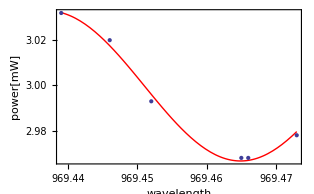

```mathematica
Clear["Global`*"]

data="
465nm, 2.968mW,
452nm, 2.993mW,
446nm, 3.020 mW,
439nm, 3.032mW,
466nm, 2.968mW,
473nm, 2.978mW,
";

power=StringSplit[data,{"nm,","mW,"}];
power=ToExpression[power[[2Range[(Length[power]-1)/2]]]];

wavelength=StringSplit[data,{"nm,","mW,"}];
wavelength=969+ToExpression[wavelength[[2Range[(Length[wavelength]-1)/2]-1]]]/10^3;

power=Thread[{wavelength, power}];
fitfn1=A Sin[2π x/T + ϕ]+offs;
{A0,T0,ϕ0,offs0}={.1,.07,0,3.01};
fit1=FindFit[power,fitfn1,{{A,A0},{T,T0},{ϕ,ϕ0},{offs,offs0}},x];

Show[{
Plot[fitfn1/.fit1,{x,Min[wavelength],Max[wavelength]},PlotStyle->{Red,Thick},Axes->False,Frame->True,FrameLabel->{"wavelength","power[mW]","T = "<>ToString[T/.fit1]<>"nm, pkpk devation="<>ToString[100 2A/offs/.fit1]<>"%"}],
ListPlot[power]
}]
```